# Spiral Structure

## Radial Dependency

First of all we assume that the spiral will be a log spiral, this means that R = aExp[kϕ].  This has the nice property that the pitch angle α, has constant value tanα = k (i.e. smaller k, tighter winding). It is also worth noting that a is just a phase

We also need to know how the density varies along the spiral, for this we take a simple ansatz inspired by the tapered Mestel disk

{{r→ρ}}

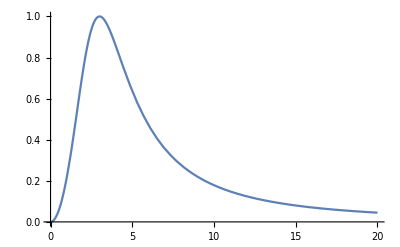

```mathematica
A[r_, ρ_, μ_] := 2/(1+(r/ρ)^μ)(r/ρ)^(μ/2);
Simplify[D[A[r,ρ,μ],r]];
Solve[%==0,r]
Plot[A[r,3, 4], {r,0,20}]
```

If we assume that μ/ν=2, then this has the nice property that the maximum value of A is at r=ρ and therefore that A(ρ) = 1/2(ρ/σ)^ν. Assuming this and deciding to normalise so that the maximum is always 1, we can eliminate σ and ν. This leaves two parameters (plus the overall density). 

Putting this all together means that we get,
	ρ(R, ϕ) = A(R)cos[m(ϕ - 1/k log(r/a))]
where for quadruple spiral we take m = 2.

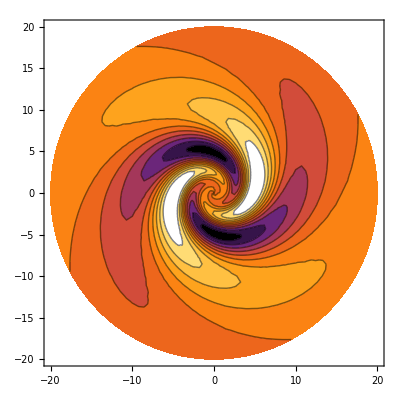

```mathematica
With[{k =.5, a = 1,m=2},ContourPlot[A[r,5, 4]Cos[m(phi -1/k Log[r/a])]/.{r->Norm[{x,y}],phi->ArcTan[x,y]},{x,-20,20},{y,-20,20},Contours->10,ContourLines->True,RegionFunction->(#1^2+#2^2<400&),ColorFunction->"SunsetColors"]]
```

```mathematica
Integrate[x/((x^2+y^2-2x y Cos[θ])^(1/2)),{θ,0,2π}]
```

ConditionalExpression[x ((2 EllipticK[-(4 x y)/(x-y)^2])/(√((x-y)^2))+(2 EllipticK[(4 x y)/(x+y)^2])/(√((x+y)^2))),(Re[x/y+y/x]≥2||Re[x/y+y/x]≤-2||x/y+y/x∉ℝ)&&Re[(x-y)^2]>0&&Re[(x+y)^2]>0]

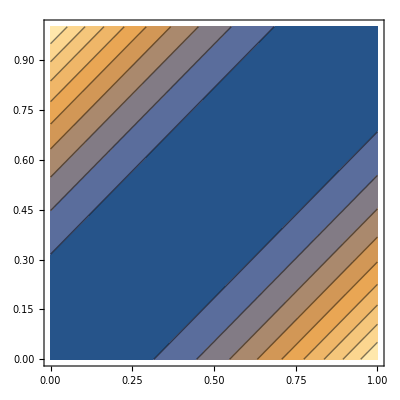

```mathematica
ContourPlot[x^2+y^2-2x y, {x,0,1}, {y,0,1}]
```

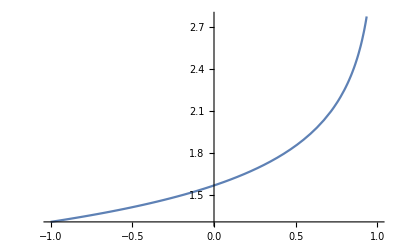

```mathematica
Plot[EllipticK[θ],{θ,-1,1}]
```

```mathematica
NIntegrate[(1+0.1 Sin[θ]^2)^(-1/2),{θ,0,π}]
2NIntegrate[(1+0.1 Sin[θ]^2)^(-1/2),{θ,0,π*0.5}]
```

3.06719

3.06719

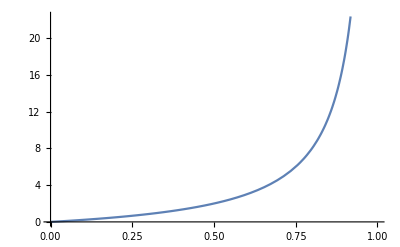

```mathematica
Plot[2 x/(1-x),{x,0,1}]
```

```mathematica
NIntegrate[x/((x^2+y^2-2x y Cos[θ])^(1/2)),{θ,0,2π}];
```